## Find the maximal values for the Wigner-𝒟 functions

```mathematica
ClearAll["Global`*"]
```

### Constants

```mathematica
spin=3;
angles={π/2,π/5,π/7};
```

### Fixed M

```mathematica
Kstates[spin_,M_,angles_]:=Table[Re[WignerD[{spin,M,K},angles[[1]],angles[[2]],angles[[3]]]],{K,-spin,spin,1}];
```

### Fixed K

```mathematica
Mstates[spin_,K_,angles_]:=Table[Re[WignerD[{spin,M,K},angles[[1]],angles[[2]],angles[[3]]]],{M,-spin,spin,1}];
```

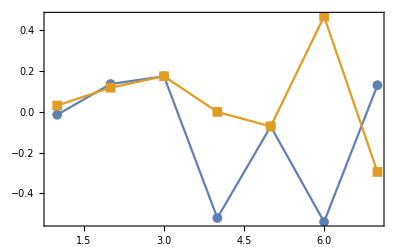

```mathematica
ListPlot[{N[Mstates[spin,1,angles]],N[Kstates[spin,1,angles]]},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,PlotRange->Full]
```